# Population simuulations

## Supplementary material Sabine C. Fischer, Elena Corujo-Simón, Joaquín Lilao, Ernst H.K. Stelzer and Silvia Muñoz-Descalzo, “The transition from local to global patterns governs the differentiation of mouse blastocysts“

The model has three parameters:
- proportion of NANOG positive cells 
- proportion of GATA6 positive cells 
- starting number of neighbours for assigning high NANOG levels

Output of the model:
- Proportions of correctly assigned cells
- Population composition
- neighbours distribution

## Initialisation

```mathematica
<<(FileNameJoin[{NotebookDirectory[],"FourPopulationModel.m"}])
```

## Data

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeaturesSaiz"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.Import[#]))&/@finalFNames}];
```

```mathematica
posStagesEmbryos=Table[Position[staging,i][[All,1]],{i,{"3.5ncb","4.0ncb","4.5ncb"}}];
```

## Simulation for wild type embryos (Fig 6 B; Fig 7 D analogous)

```mathematica
nucleiFeaturesEarly=nucleiFeatures[[posStagesEmbryos[[1]]]];
```

```mathematica
dcgGraphsEarly=dcgGraphs[[posStagesEmbryos[[1]]]];
```

pGata6 = 85 %, pNANOG = 82 %, startNumNeigh = 9

```mathematica
scanModel[nucleiFeaturesEarly,dcgGraphsEarly,0.85,0.82,9]
```

C:\Users\saf75nu\Documents\Projekte\ms mouse embryo\RoyalSocietyOpen\Supplementary material\ModelSimulation\scan2019-10-29g0.85n0.82s9.mx

```mathematica
fName=FileNameJoin[{NotebookDirectory[],"ModelSimulation","scan2019-10-29g0.85n0.82s9.mx"}];
```

```mathematica
popCount=({"propGata6"/.#,"propNanog"/.#,Total["populationCount"/.#]}&@Import[fName])
```

{0.85,0.82,{30.46,808.39,140.61,177.54}}

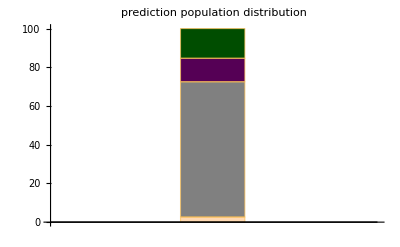

```mathematica
Labeled[BarChart[popCount[[-1]],BarSpacing->1,ChartLayout->"Percentile",ImageSize->400,ChartStyle->{Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]},ChartLabels->{{"NANOG mut"},None},PlotLabel->"prediction population distribution"], SwatchLegend[{Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]},{"DN","DP","Epi progenitor","PrE progenitor"},LegendLayout->"Row"]]
```